```mathematica
Binarize[Rasterize[Style["1",FontFamily->"Courier New"]]]
```

-Graphics-

```mathematica
ImageData[%]
```

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
TableForm[%57]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

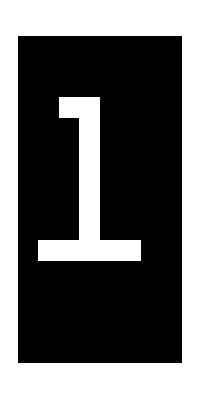

```mathematica
ArrayPlot[%57]
```

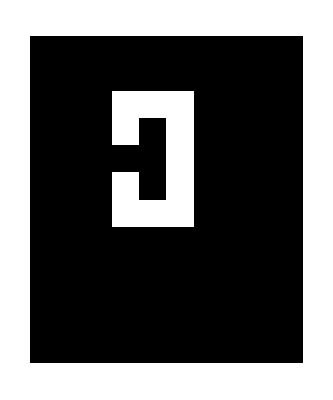
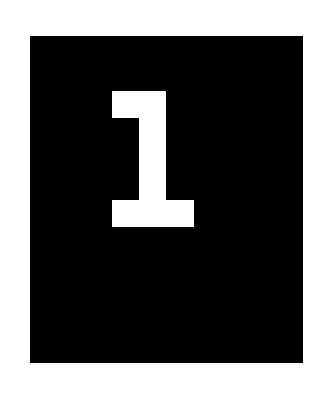
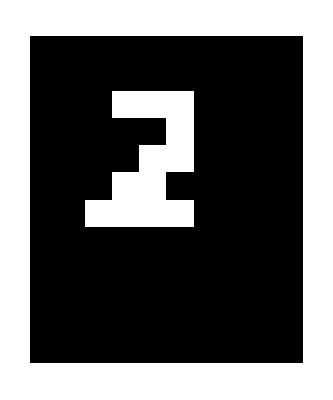
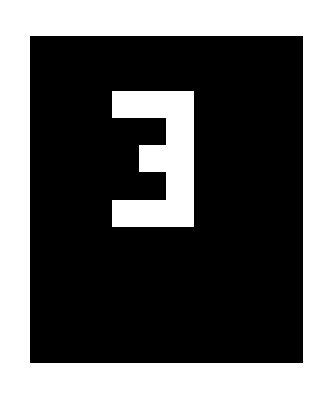
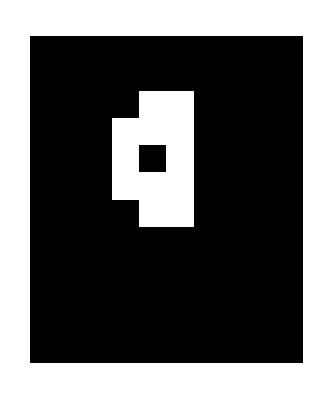
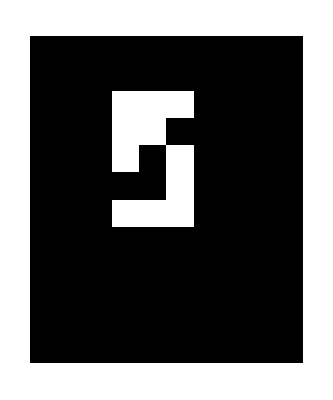
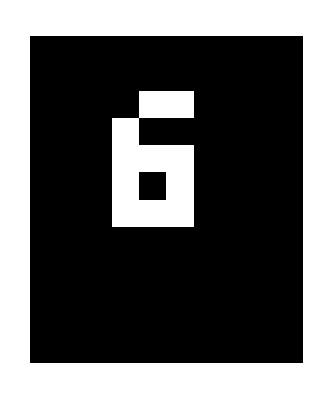
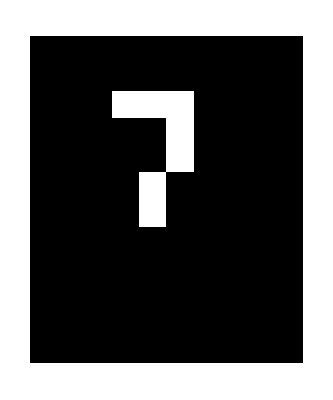

```mathematica
ArrayPlot[ImageData[Binarize[Rasterize[Style[#,FontFamily->"Courier New"],ImageSize->{10,10}]]]]&/@Range[0,9]
```

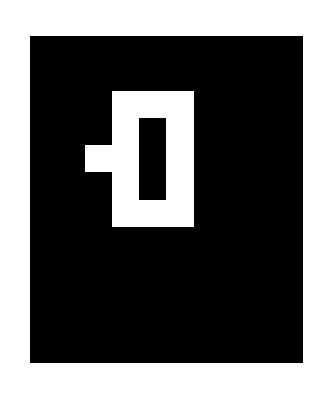
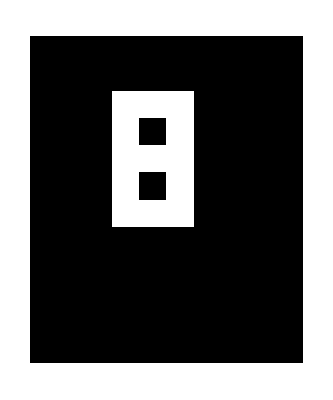
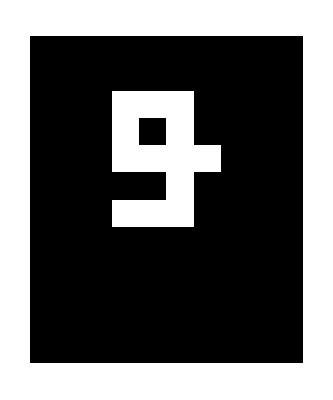
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ImageData[Binarize[Rasterize[Style[#,FontFamily->"Courier New",FontWeight->Bold],ImageSize->{10,10}]]]]&/@Range[0,9]
```

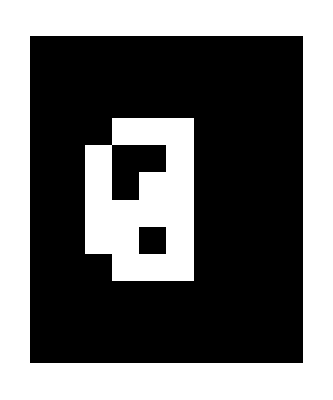
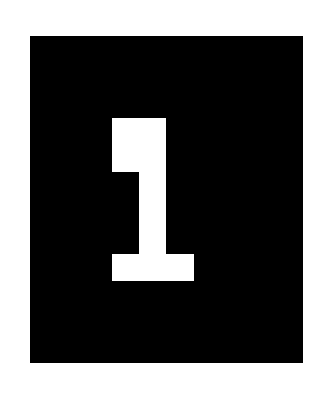
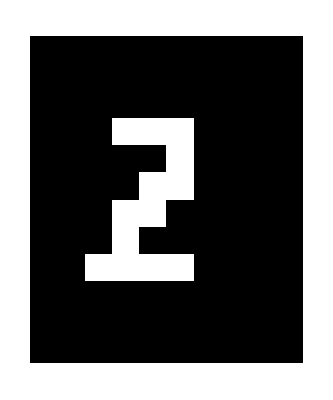
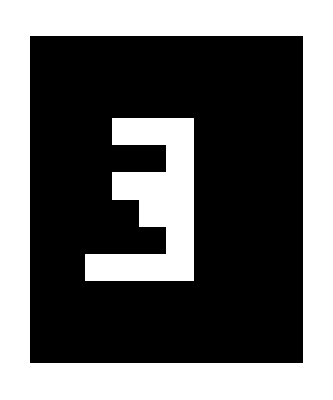
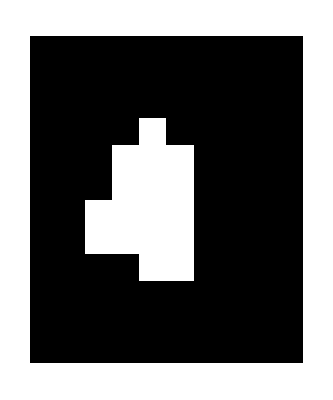
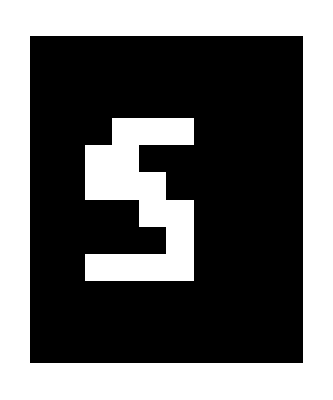
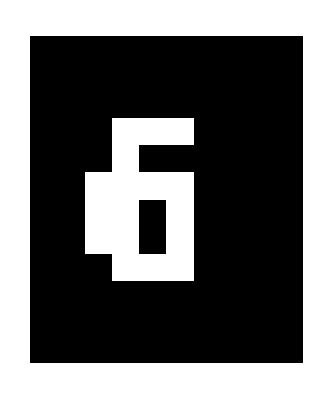
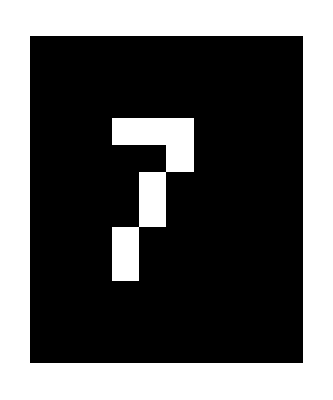

```mathematica
ArrayPlot[ImageData[Binarize[Rasterize[Style[#,FontFamily->"GB18030 Bitmap",FontWeight->Bold],ImageSize->{10,10}]]]]&/@Range[0,9]
```

```mathematica
ArrayPlot[ImageData[Binarize[Rasterize[Style[#,FontFamily->"GB18030 Bitmap",FontWeight->Bold],ImageSize->{20,20}]]]]&/@Range[0,9]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}